```mathematica
N0 = 10000
tmu = 2.1969811 * 10^-6
tpi = 2.6033 * 10^-8
n[x_] := N0/(tmu - tpi)* (Exp[-x/tmu]- Exp[-x/tpi])
```

10000

2.19698×10^-6

2.6033×10^-8

```mathematica
n[t]
```

4.60628×10^9 (-ⅇ^(-3.84128×10^7 t)+ⅇ^(-455170. t))

```mathematica
ncdf[x_]:=Integrate[n[t],{t,0,x}]
```

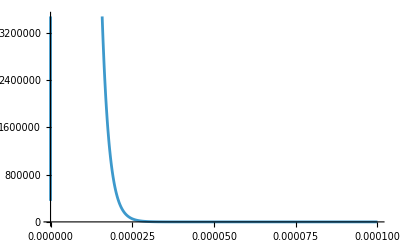

```mathematica
Plot[n[x],{x, 0, 0.0001}]
```

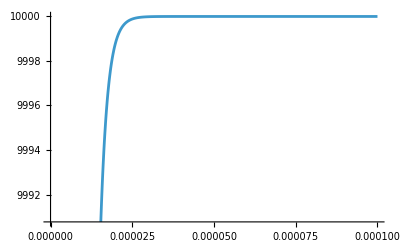

```mathematica
Plot[ncdf[x],{x, 0, 0.0001}]
```